# Caméra 1D

Voici un petit système de caméra 1D dans un monde 2D

## Pour placer un objet dans le monde...

Calcul d' une  transformation affine  dans un  monde 2D

```mathematica
Clear[place];
place[{posx_,posy_},angle_,{échellex_,échelley_}]:=TranslationTransform[{posx,posy}].RotationTransform[angle].ScalingTransform[{échellex,échelley}];
place[{posx_,posy_},angle_,échelle_]=place[{posx,posy},angle,{échelle,échelle}];
place[{posx_,posy_},angle_]=place[{posx,posy},angle,{1,1}];
place[{posx_,posy_}]=place[{posx,posy},0,{1,1}];
```

#### test

```mathematica
place[{px,py}]
place[{px,py},0,1]
place[{px,py},θ,{1,1}]
place[{px,py},θ,{sx,sy}]
```

TransformationFunction[(1 | 0 | px
0 | 1 | py
0 | 0 | 1)]

TransformationFunction[(1 | 0 | px
0 | 1 | py
0 | 0 | 1)]

TransformationFunction[(Cos[θ] | -Sin[θ] | px
Sin[θ] | Cos[θ] | py
0 | 0 | 1)]

TransformationFunction[(sx Cos[θ] | -sy Sin[θ] | px
sx Sin[θ] | sy Cos[θ] | py
0 | 0 | 1)]

## Primitives 2D

Pour l' instant,  un simple carré ou cercle...

```mathematica
unCarré[]:={{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}};
unCercle[]:=Table[{Cos[t],Sin[t]},{t,0,2Pi-Pi/1000,Pi/16}];
```

#### testInverseFunction[w2cA]

```mathematica
(place[{0,0},Pi/4].place[{1,2}])@unCarré[]
```

{{-1/(√2),1/(√2)},{-3/(√2),3/(√2)},{-1/(√2),5/(√2)},{1/(√2),3/(√2)},{-1/(√2),1/(√2)}}

## Un monde complet

Le monde est une liste de  primitives avec chacun une couleur et opacité .

```mathematica
monde={
<|"couleur" ->Red,"lignes"->place[{2,2},Pi/4]@unCarré[]|>
};
monde={
<|"couleur" ->Red,"lignes"->place[{0,2},0]@unCercle[]|>
};
monde={
<|"couleur" ->Red,"opacite"->0.2,"lignes"->place[{0,2},0]@unCarré[]|>,
<|"couleur" ->Blue,"opacite" ->0.2,"lignes"->place[{1,1},0]@unCercle[]|>
};
```

## Visualiser le monde

```mathematica
see[e_]:={
If[KeyExistsQ[e,"couleur"],e[["couleur" ]],Black],If[KeyExistsQ[e,"opacite"],Opacity[e[["opacite"]]],Opacity[1]],Polygon[e[["lignes" ]]]};

seeMonde[monde_,{{xmin_,xmax_},{ymin_,ymax_}}]:=Block[{},(
Graphics[{
GrayLevel[0.8],Rectangle[{xmin,ymin},{xmax,ymax}],
GrayLevel[0.9],Thick,
Line[{{0,ymin},{0,ymax}}],
Line[{{xmin,0},{xmax,0}}],
see/@monde
}]
)]
```

#### test

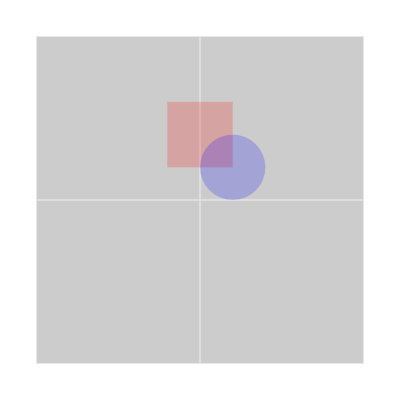

```mathematica
seeMonde[monde,{{-5,5},{-5,5}}]
```

## Camera 1D

une camera  est  une matrice  projective  2 x 3 (2dproj->1dproj).
On va utiliser w2c pour world to cam  et c2w pour  cam  to  world
Si on a deux cameras,  A et B,  on  va  avoir    w2cA et w2cB, et aussi cA2w et cB2w

w : world
c : camera  (cA, cB,  ...)
i  : image (iA, iB, ...)

Les  parametres internes contiennent une distance focale f et un centre c:
(f | c
0 | 1)

```mathematica
interne=AffineTransform[({{50, 50}, {0, 1}})];
cA2w=place[{-1,-3},-Pi/8.]
iA2w=cA2w.InverseFunction[interne]
w2cA=InverseFunction[place[{-1,-3},-Pi/8.]]
w2iA=interne.w2cA
```

TransformationFunction[(0.92388 | 0.382683 | -1.
-0.382683 | 0.92388 | -3.
0. | 0. | 1.)]

TransformationFunction[(0.0184776 | -0.541196 | -1.
-0.00765367 | 1.30656 | -3.
0. | 0. | 1.)]

TransformationFunction[(0.92388 | -0.382683 | -0.224171
0.382683 | 0.92388 | 3.15432
0. | 0. | 1.)]

TransformationFunction[(65.3281 | 27.0598 | 146.508
0.382683 | 0.92388 | 3.15432
0. | 0. | 1.)]

## Affichage de la camera

```mathematica
e2p[v_]:=Append[v,1];
p2e[v_]:=Delete[v,-1]/v[[-1]];
```

```mathematica
seeCam[w2i_TransformationFunction,width_,depth_]:=Block[{i2w,coinsCam,coinsW},(
i2w=InverseFunction[w2i];
coinsCam={{0,1}*depth,{0,0},{width,1}*depth};
coinsW=i2w[coinsCam];
Graphics[{
PointSize[0.025],
Blue,Point[coinsW[[2]]],
Opacity[0.4],Polygon[coinsW]
}]
)]
```

#### test

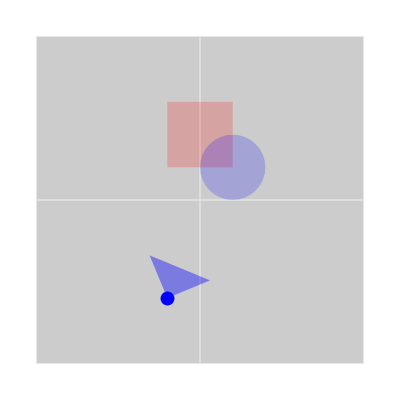

```mathematica
Show[
seeMonde[monde,{{-5,5},{-5,5}}],
seeCam[w2iA,100,1]
]
```

## Prise d' une photo

On prend une photo d' un segment, qui  est une liste  de points  du monde

```mathematica
photo[w2i_TransformationFunction,segment_]:=Block[{p,q,m},(
m=TransformationMatrix[w2i];
p=(m.e2p[#])&/@segment;
q=p/p[[All,2]];
q[[All,{1,3}]]; (*  la position  X  et 1/Z *)
{#[[1]],1/#[[3]]}&/@q
)]
```

#### test

```mathematica
v=photo[w2iA,monde[[1,"lignes" ]]]
vg={#[["couleur" ]],Polygon[photo[w2iA,#[["lignes" ]]]]}&/@monde
```

{{29.2893,3.69552},{29.2893,5.54328},{46.4466,6.30864},{53.5534,4.46088},{29.2893,3.69552}}

{{RGBColor[1, 0, 0],Polygon[…]},{RGBColor[0, 0, 1],Polygon[…]}}

from est {x, d}
Le  premier pixel  est 0..1,ensuite 1..2,etc... w-1..w

```mathematica
zrange=MinMax[Table[(List@@vg[[i,2]])[[1,All,2]],{i,1,Length[vg]}]]
zresol=0.1
(zrange[[2]]-zrange[[1]])/zresol/100
```

{3.46088,6.30864}

0.1

0.284776

```mathematica
xz=Rasterize[Graphics[{Opacity[0.2],vg},AspectRatio->0.284776,PlotRange->{{0,100},zrange}],RasterSize->{100,Automatic},Background->None]
```

-Graphics-

```mathematica
zxd=Transpose[ImageData[xz]];
Dimensions[zxd]
```

{100,29,4}

```mathematica
opacity[v_]:=1-Ramp[1-Accumulate[v]];
alpha[opa_]:=
opa-Prepend[opa[[1;;-2]],0.];
```

```mathematica
opa=opacity[{0.15,0.1,0.4,0.3,0.6,0.8,0.2,0.1}]
alpha[opa]
```

{0.15,0.25,0.65,0.95,1.,1.,1.,1.}

{0.15,0.1,0.4,0.3,0.05,0.,0.,0.}

```mathematica
Clear[densify];densify[rgba_,background_:{0.0,0.1,0.2}]:=Block[{r,g,b,a,opa,aa},(
{r,g,b,a}=Transpose[Append[rgba,Append[background,1.]]];
opa=opacity[a];
aa=alpha[opa];
Transpose[{r.aa,g.aa,b.aa,opa[[-2]]}]
)];
```

```mathematica
img=densify[#,{1,1,0}]&/@zxd;
ii=Image[{RGBColor/@img},ImageSize->Scaled[0.9]]
```

-Graphics-

zresol :  resolution en Z dans le  rendu .  ideal  :  0.1 ou 0.01

## Rendu d' une photo 1D

```mathematica
snapshot[w2i_TransformationFunction,monde_,width_,zresol_]:=Block[{vg,xz,zxd,iid,ii,zmin,zmax,ratio,nbz},(
vg={
#[["couleur" ]],
Opacity[If[KeyExistsQ[#,"opacite"],#[["opacite"]],1]],
Polygon[photo[w2i,#[["lignes" ]]]]
}&/@monde;
{zmin,zmax}=MinMax[Table[(List@@vg[[i,3]])[[1,All,2]],{i,1,Length[vg]}]];
zmin=Max[0,zmin];
zmax=Max[zmax,zmin+1];
ratio=Min[Max[(zmax-zmin)/zresol/width,0.1],3];
xz=Rasterize[Graphics[{Opacity[0.2],vg},AspectRatio->ratio,PlotRange->{{0,width},{zmin,zmax}}],RasterSize->{width,Automatic},Background->None];
zxd=Transpose[ImageData[xz]];
nbz=Dimensions[zxd][[2]];
(* ajuste alpha pour le nb  de  pixels en z ? *) 
iid=densify[#,{1,1,1}]&/@zxd;
Image[{RGBColor/@iid},ImageSize->Scaled[1]]
)]
```

#### test

```mathematica
snapshot[w2iA,monde,100,0.1]
```

-Graphics-

## Full Test

```mathematica
monde={
<|"couleur" ->Red,
"opacite" ->0.05,
"lignes"->place[{0,1},0]@unCarré[]|>,
<|"couleur" ->Blue,
"opacite" ->0.3,
"lignes"->place[{1,0},0]@unCercle[]|>
};
```

c2i est param  interne

```mathematica
c2i=LinearFractionalTransform[({{50, 50, 0}, {0, 1, 0}, {0, 0, 1}})];
i2c=InverseFunction[c2i];
```

```mathematica
cB2w=Table[place[{Cos[θ],Sin[θ]}*4.5,θ+Pi/2],{θ,0,2Pi-Pi/1000,Pi/32}];

iB2w=(#.i2c)&/@cB2w;
w2iB=InverseFunction/@iB2w;
```

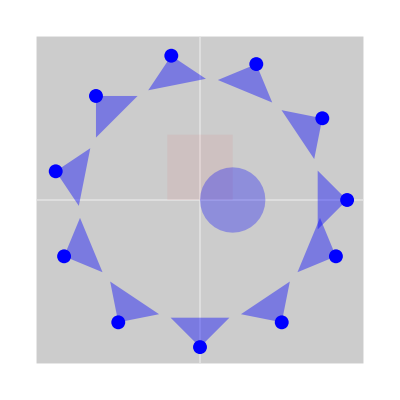

```mathematica
Show[
seeMonde[monde,{{-5,5},{-5,5}}],
seeCam[#,100,0.9]&/@w2iB[[1;;-1;;6]]
]
```

```mathematica
is=snapshot[#,monde,100,0.1]&/@w2iB;
```

```mathematica
is[[1]]
```

-Graphics-

```mathematica
Image[ImageAssemble[Transpose[{is}]],ImageSize->Scaled[0.9]]
```

-Graphics-